# Bessel Transform Implementation.

```mathematica
SphericalBesselJ[2,3]
```

SphericalBesselJ[2,3]

```mathematica
N[SphericalBesselJ[2,3]]
```

0.298637

```mathematica
SphericalBesselJ[2,x]
```

SphericalBesselJ[2,x]

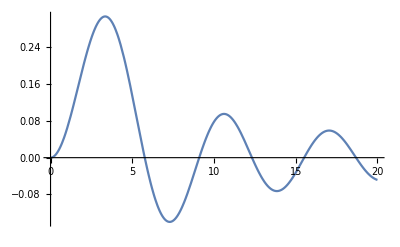

```mathematica
Plot[SphericalBesselJ[2,x],{x,0,20}]
```

```mathematica
SphericalBesselJ[0.1666666666666,0.5]
```

0.750299

```mathematica
NumberForm[0.7502987701804948,16]
```

0.7502987701804948

```mathematica
SphericalBesselJ[0.1666666666666,1.5]
```

0.651585

```mathematica
NumberForm[0.6515852144813531,16]
```

0.6515852144813531

```mathematica
SphericalBesselJ[0.1666666666666,2.5]
```

0.30693

```mathematica
NumberForm[0.3069299146132758,16]
```

0.3069299146132758

```mathematica
SphericalBesselJ[0.1666666666666,3.5]
```

-0.0353128

```mathematica
NumberForm[-0.03531278634299662,16]
```

-0.03531278634299662

```mathematica
SphericalBesselJ[0.1666666666666,4.5]
```

-0.200257

```mathematica
NumberForm[-0.20025662282195283,16]
```

-0.2002566228219528

```mathematica
SphericalBesselJ[0.1666666666666,5.5]
```

-0.155885

```mathematica
NumberForm[-0.1558846349198312,16]
```

-0.1558846349198312

```mathematica
SphericalBesselJ[0.1666666666666,6.5]
```

-0.00464891

```mathematica
NumberForm[-0.0046489085978687825,16]
```

-0.004648908597868783

```mathematica
SphericalBesselJ[0.1666666666666,7.5]
```

0.109917

```mathematica
NumberForm[0.10991685584445024,16]
```

0.1099168558444502

```mathematica
Made mistake above. Its J(l,kr)
```

```mathematica
SphericalBesselJ[2,0.1666666666666*7.5]
```

0.0930337

```mathematica
NumberForm[0.09303374404672973,16]
```

0.0930337440467297

```mathematica
NumberForm[0.07189193076641275,16]
```

0.07189193076641275

```mathematica
NumberForm[0.0527337826212236,16]
```

0.0527337826212236

```mathematica
NumberForm[0.03601664614108058,16]
```

0.03601664614108058

```mathematica
NumberForm[0.022138994068736095,16]
```

0.0221389940687361

```mathematica
NumberForm[0.011431236718868237,16]
```

0.01143123671886824

```mathematica
NumberForm[0.0041480977393578205,16]
```

0.00414809773935782

```mathematica
NumberForm[0.0004627333629297398,16]
```

0.0004627333629297397

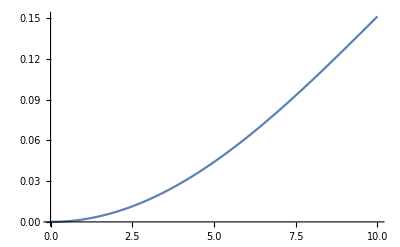

```mathematica
Plot[SphericalBesselJ[2,0.1666666666666 x],{x,0,10}]
```

## Getting the feel of different types of Bessel function in out transform domain with delta_r=1 (Nyquist Frequency)

```mathematica
Plot of the Bessel functions in out domains.
```

```mathematica
SphericalBesselJ[2,1.666666666666*x]
```

SphericalBesselJ[2,1.66667 x]

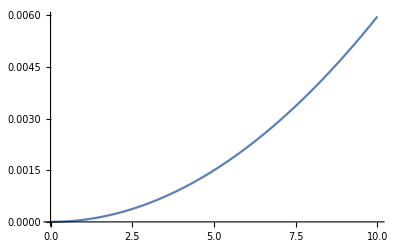

```mathematica
Plot[SphericalBesselJ[2,0.03*x],{x,0,10}]
```

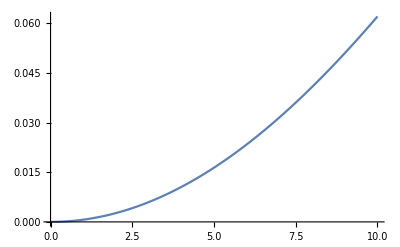

```mathematica
Plot[SphericalBesselJ[2,.10*x],{x,0,10}]
```

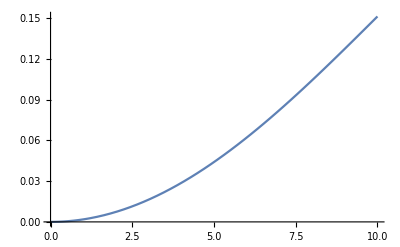

```mathematica
Plot[SphericalBesselJ[2,0.16666*x],{x,0,10}]
```

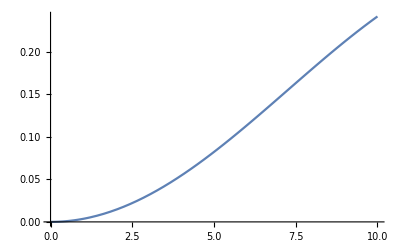

```mathematica
Plot[SphericalBesselJ[2,0.2333*x],{x,0,10}]
```

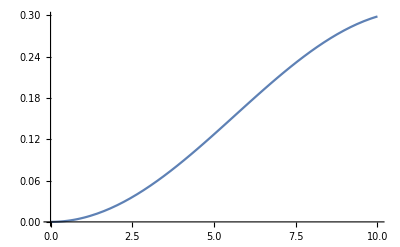

```mathematica
Plot[SphericalBesselJ[2,0.2999*x],{x,0,10}]
```

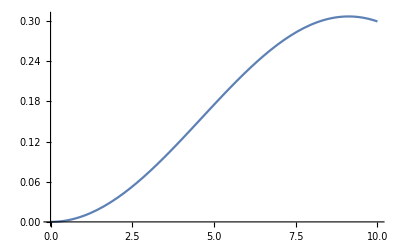

```mathematica
Plot[SphericalBesselJ[2,.3666*x],{x,0,10}]
```

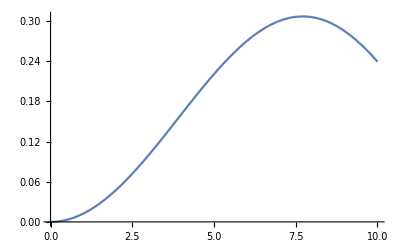

```mathematica
Plot[SphericalBesselJ[2,.4333*x],{x,0,10}]
```

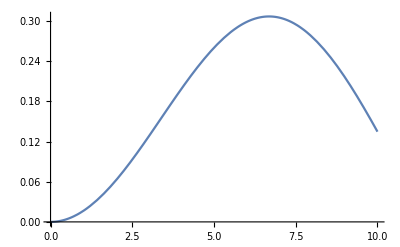

```mathematica
Plot[SphericalBesselJ[2,.5000*x],{x,0,10}]
```

```mathematica
420*SphericalBesselJ[2,0.0333*x]+
-420*SphericalBesselJ[2,0.1*x]+
133.669*SphericalBesselJ[2,0.1666666666*x]+
15.84*SphericalBesselJ[2,0.2333333333*x]+
19*SphericalBesselJ[2,0.2999999999*x]+
-35*SphericalBesselJ[2,0.3666666666*x]+
20*SphericalBesselJ[2,0.433333333333*x]+
1*SphericalBesselJ[2,0.5000000*x]
```

420 SphericalBesselJ[2,0.0333 x]-420 SphericalBesselJ[2,0.1 x]+133.669 SphericalBesselJ[2,0.166667 x]+15.84 SphericalBesselJ[2,0.233333 x]+19 SphericalBesselJ[2,0.3 x]-35 SphericalBesselJ[2,0.366667 x]+20 SphericalBesselJ[2,0.433333 x]+SphericalBesselJ[2,0.5 x]

```mathematica
Plot of this type.
```

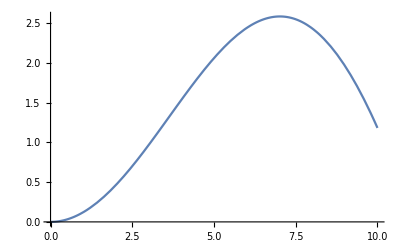

```mathematica
Plot[%121,{x,0,10}]
```

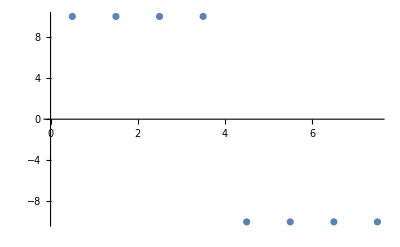

```mathematica
ListPlot[{{0.5,10},{1.5,10},{2.5,10},{3.5,10},{4.5,-10},{5.5,-10},{6.5,-10},{7.5,-10}}]
```

```mathematica
Plot for this type.
```

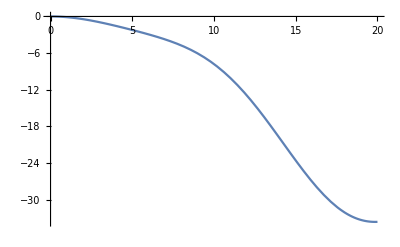

```mathematica
Plot[%112,{x,0,20}]
```

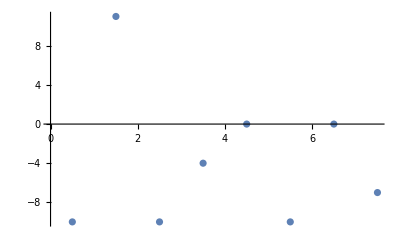

```mathematica
ListPlot[{{0.5,-10},{1.5,11},{2.5,-10},{3.5,-4},{4.5,0},{5.5,-10},{6.5,0},{7.5,-7}}]
```

```mathematica
.01049830510094196*SphericalBesselJ[2,6.6666*x]+
-.01051749754042095*SphericalBesselJ[2,20*x]+
0.003341728455635268*SphericalBesselJ[2,33*x]+
0.00039684687671955114*SphericalBesselJ[2,46*x]+
0.00049591833814246458*SphericalBesselJ[2,60*x]+
-0.00089335651661860802*SphericalBesselJ[2,73*x]+
0.00051186623633481807*SphericalBesselJ[2,86*x]+
0.000036665942667272192*SphericalBesselJ[2,100*x]
```

0.0104983 SphericalBesselJ[2,6.6666 x]-0.0105175 SphericalBesselJ[2,20 x]+0.00334173 SphericalBesselJ[2,33 x]+0.000396847 SphericalBesselJ[2,46 x]+0.000495918 SphericalBesselJ[2,60 x]-0.000893357 SphericalBesselJ[2,73 x]+0.000511866 SphericalBesselJ[2,86 x]+0.0000366659 SphericalBesselJ[2,100 x]

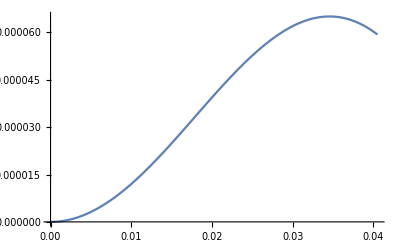

```mathematica
Plot[%147,{x,0,0.040499999161809683}]
```

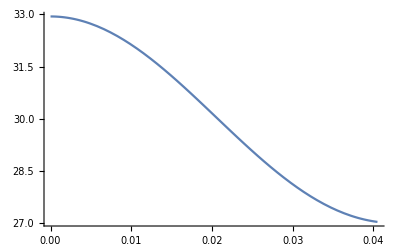

```mathematica
Plot[%139,{x,0,0.040499999161809683}]
```

```mathematica
RECHECK OF CALCULATION
```

```mathematica
f[k_,x_]:=SphericalBesselJ[1,k*x]
```

```mathematica
DynamicModule[{l,k,x},Column[{Dynamic@Plot[SphericalBesselJ[l,k*x],{x,0,10},PlotRange->{All,{-1,1}}],Slider[Dynamic@l,{0,4,1}],Slider[Dynamic@k,{0,10}]}]]
```

```mathematica
f[0.35714285714285715,0.5]
```

0.0593342

```mathematica
NumberForm[0.05933421749273684,16]
```

0.05933421749273684

```mathematica
f[0.35714285714285715,1.5]
```

0.173499

```mathematica
NumberForm[0.17349886004614506,16]
```

0.1734988600461451

```mathematica
f[0.35714285714285715,2.5]
```

0.274559

```mathematica
NumberForm[0.2745586648836568,16]
```

0.2745586648836568

```mathematica
f[0.35714285714285715,3.5]
```

0.355092

```mathematica
NumberForm[0.3550922664713602,16]
```

0.3550922664713602

```mathematica
0.47614897033684234*f[0.0714285714285714,x]+0.20089102494066821*f[0.21428571428571427,x]+-0.14777344391103076*f[0.35714285714285715,x]+-0.039569803268302700*f[0.50000000000000000,x]
```

0.476149 SphericalBesselJ[1,0.0714286 x]+0.200891 SphericalBesselJ[1,0.214286 x]-0.147773 SphericalBesselJ[1,0.357143 x]-0.0395698 SphericalBesselJ[1,0.5 x]

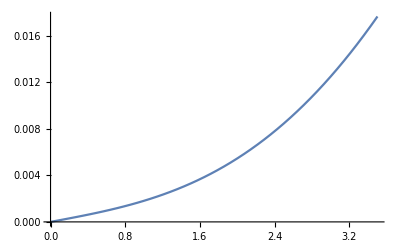

```mathematica
Plot[%63,{x,0,3.5}]
```

```mathematica
0.47614897033684234 SphericalBesselJ[1,0.0714285714285714 x]+0.2008910249406682 SphericalBesselJ[1,0.21428571428571427 x]-0.24777344391103076 SphericalBesselJ[1,0.35714285714285715 x]-0.0395698032683027 SphericalBesselJ[1,0.5 x]
```

```mathematica
0.17614897033684234 SphericalBesselJ[1,0.0714285714285714 x]+0.2008910249406682 SphericalBesselJ[1,0.21428571428571427 x]-0.24777344391103076 SphericalBesselJ[1,0.35714285714285715 x]-0.0395698032683027 SphericalBesselJ[1,0.5 x]
```

```mathematica
0.17614897033684235 SphericalBesselJ[1,0.0714285714285714 x]+0.2008910249406682 SphericalBesselJ[1,0.21428571428571427 x]+0.24777344391103076 SphericalBesselJ[1,0.35714285714285715 x]-0.0395698032683027 SphericalBesselJ[1,0.5 x]
```

```mathematica
0.47614897033684235 SphericalBesselJ[1,0.0714285714285714 x]+0.2008910249406682 SphericalBesselJ[1,0.21428571428571427 x]-0.24777344391103076 SphericalBesselJ[1,0.35714285714285715 x]-0.0395698032683027 SphericalBesselJ[1,0.5 x]
```

0.476149 SphericalBesselJ[1,0.0714286 x]+0.200891 SphericalBesselJ[1,0.214286 x]-0.247773 SphericalBesselJ[1,0.357143 x]-0.0395698 SphericalBesselJ[1,0.5 x]

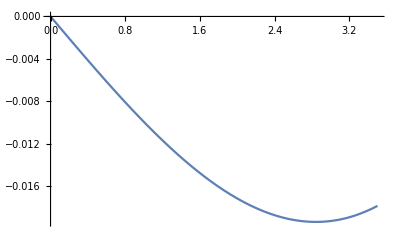

```mathematica
Plot[%13,{x,0,3.5}]
```

```mathematica
5/7/17
```

```mathematica
Roots[SphericalBesselJ[1,k*3.5]==0,k]
```

Roots::neq: SphericalBesselJ[1,3.5 k] is expected to be a polynomial in the variable k.

Roots[SphericalBesselJ[1,3.5 k]==0,k]

```mathematica
BesselJZero[1,{1,2,3,4,5,6,7,8,9,10}]
```

{BesselJZero[1,1],BesselJZero[1,2],BesselJZero[1,3],BesselJZero[1,4],BesselJZero[1,5],BesselJZero[1,6],BesselJZero[1,7],BesselJZero[1,8],BesselJZero[1,9],BesselJZero[1,10]}

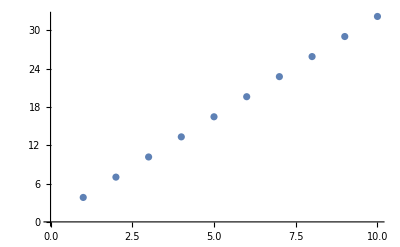

```mathematica
ListPlot[{BesselJZero[1,1],BesselJZero[1,2],BesselJZero[1,3],BesselJZero[1,4],BesselJZero[1,5],BesselJZero[1,6],BesselJZero[1,7],BesselJZero[1,8],BesselJZero[1,9],BesselJZero[1,10]}]
```

```mathematica
{BesselJZero[1,1],BesselJZero[1,2],BesselJZero[1,3],BesselJZero[1,4]}
```

{BesselJZero[1,1],BesselJZero[1,2],BesselJZero[1,3],BesselJZero[1,4]}

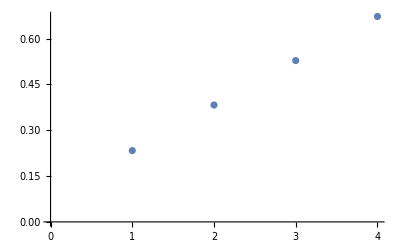

```mathematica
ListPlot[{BesselJZero[2,1]/3.5/2/Pi,BesselJZero[2,2]/3.5/2/Pi,BesselJZero[2,3]/3.5/2/Pi,BesselJZero[2,4]/3.5/2/Pi}]
```

```mathematica
BesselJZero[1,3]
```

BesselJZero[1,3]

```mathematica
N[BesselJZero[1,3]]
```

```mathematica
10.173468135062722/2/Pi/3.5
```

0.462616

```mathematica
N[BesselJZero[1,1]]
```

3.83171

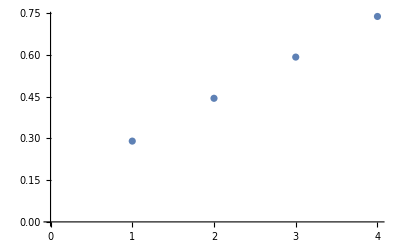

```mathematica
ListPlot[{BesselJZero[3,1]/3.5/2/Pi,BesselJZero[3,2]/3.5/2/Pi,BesselJZero[3,3]/3.5/2/Pi,BesselJZero[3,4]/3.5/2/Pi}]
```

```mathematica
TRY 1:
```

```mathematica
f[k_,x_]:=SphericalBesselJ[1,k*x]
```

```mathematica
f[0.35714285714285715,3.5]
```

0.355092

```mathematica
NumberForm[0.09303374404679564,16]
```

0.0930337440467956

```mathematica
NumberForm[0.05018619335987668,16]
```

0.05018619335987669

```mathematica
NumberForm[0.018743560698120366,16]
```

0.01874356069812037

```mathematica
NumberForm[0.0021210125845030734,16]
```

0.002121012584503073

```mathematica
-0.49053364031509206*f[0.0714285714285714,x]+0.38876107481048594*f[0.21428571428571427,x]+
-0.12865436689321164*f[0.35714285714285715,x]+
0.074385691972614271*f[0.50000000000000000,x]
```

-0.490534 SphericalBesselJ[2,0.0714286 x]+0.388761 SphericalBesselJ[2,0.214286 x]-0.128654 SphericalBesselJ[2,0.357143 x]+0.0743857 SphericalBesselJ[2,0.5 x]

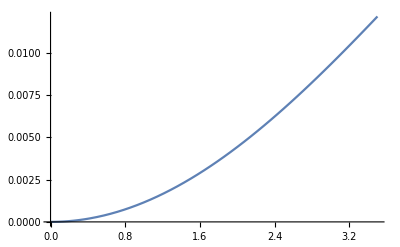

```mathematica
Plot[%37,{x,0,3.5}]
```

```mathematica
g[x_]:=-0.49053364031509206*f[0.0714285714285714,x]+0.38876107481048594*f[0.21428571428571427,x]+
-0.12865436689321164*f[0.35714285714285715,x]+
0.074385691972614271*f[0.50000000000000000,x]
```

```mathematica
Function[x,-0.49053364031509206 f[0.0714285714285714,x]+0.38876107481048594 f[0.21428571428571427,x]-0.12865436689321164 f[0.35714285714285715,x]+0.07438569197261427 f[0.5,x]]
```

Function[x,-0.490534 f[0.0714286,x]+0.388761 f[0.214286,x]-0.128654 f[0.357143,x]+0.0743857 f[0.5,x]]

```mathematica
Function[x,-0.49053364031509206 f[0.0714285714285714,x]+0.38876107481048594 f[0.21428571428571427,x]-0.12865436689321164 f[0.35714285714285715,x]+0.07438569197261427 f[0.5,x]][2.5]
```

0.00671005

```mathematica
Function[x,-0.49053364031509206 f[0.0714285714285714,x]+0.38876107481048594 f[0.21428571428571427,x]-0.12865436689321164 f[0.35714285714285715,x]+0.07438569197261427 f[0.5,x]][1.5]
```

0.00255057

```mathematica
Function[x,-0.49053364031509206 f[0.0714285714285714,x]+0.38876107481048594 f[0.21428571428571427,x]-0.12865436689321164 f[0.35714285714285715,x]+0.07438569197261427 f[0.5,x]][0.5]
```

0.000291251

```mathematica
NumberForm[0.00029125069516372883,16]
```

0.0002912506951637289

```mathematica
TRY 2:
```

```mathematica
95.048041866391230*f[0.0714285714285714,x]+-80.716459661127274*f[0.21428571428571427,x]+
29.644245231995338*f[0.35714285714285715,x]+
-8.2780673106332756*f[0.50000000000000000,x]
```

95.048 SphericalBesselJ[2,0.0714286 x]-80.7165 SphericalBesselJ[2,0.214286 x]+29.6442 SphericalBesselJ[2,0.357143 x]-8.27807 SphericalBesselJ[2,0.5 x]

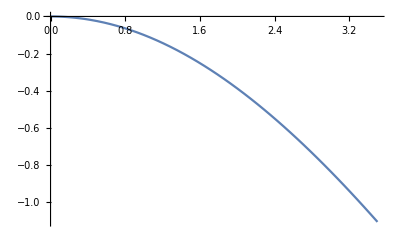

```mathematica
Plot[95.04804186639123 SphericalBesselJ[2,0.0714285714285714 x]-80.71645966112727 SphericalBesselJ[2,0.21428571428571427 x]+29.64424523199534 SphericalBesselJ[2,0.35714285714285715 x]-8.278067310633276 SphericalBesselJ[2,0.5 x],{x,0,3.5}]
```

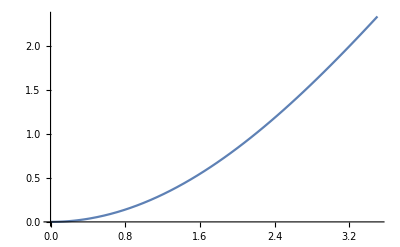

```mathematica
Plot[-102.8554362260005 SphericalBesselJ[2,0.0714285714285714 x]+81.88189579306305 SphericalBesselJ[2,0.21428571428571427 x]-23.5471391097726 SphericalBesselJ[2,0.35714285714285715 x]+12.300000128464895 SphericalBesselJ[2,0.5 x],{x,0,3.5}]
```

```mathematica
Expand[c0+c1*(t-to)+c2*(t-to)^2+c3*(t-to)^3+c4*(t-to)^4+c5*(t-to)^5,{c0,c1,c2,c3,c4,c5,to,t}]
```

c0+c1 (t-to)+c2 (t-to)^2+c3 (t-to)^3+c4 (t-to)^4+c5 (t-to)^5

```mathematica
FullSimplify[c0+c1 (t-to)+c2 (t-to)^2+c3 (t-to)^3+c4 (t-to)^4+c5 (t-to)^5]
```

c0+(t-to) (c1+(t-to) (c2+(t-to) (c3+(t-to) (c4+c5 t-c5 to))))

```mathematica
Expand[c0+(t-to) (c1+(t-to) (c2+(t-to) (c3+(t-to) (c4+c5 t-c5 to))))]
```

c0+c1 t+c2 t^2+c3 t^3+c4 t^4+c5 t^5-c1 to-2 c2 t to-3 c3 t^2 to-4 c4 t^3 to-5 c5 t^4 to+c2 to^2+3 c3 t to^2+6 c4 t^2 to^2+10 c5 t^3 to^2-c3 to^3-4 c4 t to^3-10 c5 t^2 to^3+c4 to^4+5 c5 t to^4-c5 to^5

```mathematica
Collect[%3,t]
```

c0+c5 t^5-c1 to+c2 to^2-c3 to^3+c4 to^4-c5 to^5+t^4 (c4-5 c5 to)+t^3 (c3-4 c4 to+10 c5 to^2)+t^2 (c2-3 c3 to+6 c4 to^2-10 c5 to^3)+t (c1-2 c2 to+3 c3 to^2-4 c4 to^3+5 c5 to^4)

```mathematica
TRY 2.5
```

```mathematica
0.47614897033684234*f[0.0714285714285714,x]+0.045386420410768333*f[0.21428571428571427,x]+
-0.10017383573464292*f[0.35714285714285715,x]+
-0.052217539387409119*f[0.50000000000000000,x]
```

0.476149 SphericalBesselJ[1,0.0714286 x]+0.0453864 SphericalBesselJ[1,0.214286 x]-0.100174 SphericalBesselJ[1,0.357143 x]-0.0522175 SphericalBesselJ[1,0.5 x]

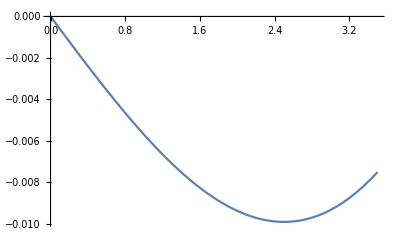

```mathematica
Plot[%22,{x,0,3.5}]
```

```mathematica
TRY 3 and mostly last. :(
CASE :EVEN
```

```mathematica
f[k_,x_]:=SphericalBesselJ[2,k*x]
```

```mathematica
f[0.21428571428571427,3.5]
```

0.236217

```mathematica
NumberForm[0.2362170815430551,16]
```

0.2362170815430551

```mathematica
NumberForm[0.17349886004614506,16]
```

0.1734988600461451

```mathematica
NumberForm[0.1060399732353563,16]
```

0.1060399732353563

```mathematica
NumberForm[0.03567330397724352,16]
```

0.03567330397724352

```mathematica
-1.3867676100426858*f[0.0714285714285714,x]+0.27446661168394293*f[0.21428571428571427,x]+
-0.0041048519691180684*f[0.35714285714285715,x]+
0.0037316014504962872*f[0.50000000000000000,x]
```

-1.38677 SphericalBesselJ[2,0.0714286 x]+0.274467 SphericalBesselJ[2,0.214286 x]-0.00410485 SphericalBesselJ[2,0.357143 x]+0.0037316 SphericalBesselJ[2,0.5 x]

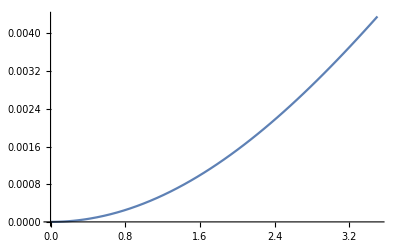

```mathematica
Plot[%36,{x,0,3.5}]
```

```mathematica
TRY 4:
CASE : ODD
```

```mathematica
f[k_,x_]:=SphericalBesselJ[3,k*x]
```

```mathematica
f[0.21428571428571427,3.5]
```

0.00389389

```mathematica
NumberForm[0.003893892730999794,16]
```

0.003893892730999794

```mathematica
NumberForm[0.0014410398029783588,16]
```

0.001441039802978359

```mathematica
NumberForm[0.0003144633750463319,16]
```

0.0003144633750463319

```mathematica
NumberForm[0.00001170640059008349,16]
```

0.00001170640059008349

-0.000895924 SphericalBesselJ[3,0.0714286 x]+0.00869508 SphericalBesselJ[3,0.214286 x]-0.00306548 SphericalBesselJ[3,0.357143 x]+0.00102069 SphericalBesselJ[3,0.5 x]

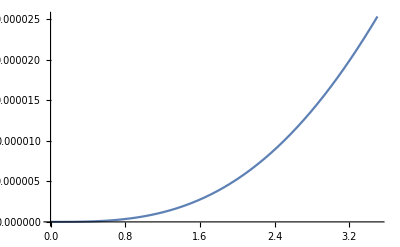

```mathematica
Plot[%48,{x,0,3.5}]
```

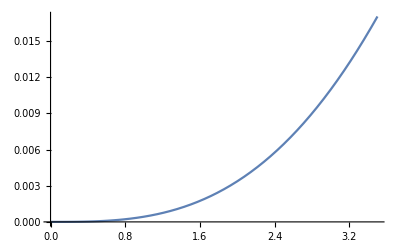

```mathematica
Plot[SphericalBesselJ[3,0.35714285714285715*x],{x,0,3.5}]
```

```mathematica
f[k_,x_]:=SphericalBesselJ[3,k*x]
```

```mathematica
f[0.50000000000000000,0.5]
```

0.000148294

```mathematica
NumberForm[0.00014829355743476835,16]
```

0.0001482935574347684

```mathematica
NumberForm[0.003893892730999794,16]
```

0.003893892730999794

```mathematica
NumberForm[0.017042709715822217,16]
```

0.01704270971582222

```mathematica
NumberForm[0.042938795299626076,16]
```

0.04293879529962608

```mathematica
-0.0099715211762826418*f[0.0714285714285714,x]+0.096416469964918927*f[0.21428571428571427,x]+
-0.032914645523244662*f[0.35714285714285715,x]+
0.010918632156254850*f[0.50000000000000000,x]
```

-0.00997152 SphericalBesselJ[3,0.0714286 x]+0.0964165 SphericalBesselJ[3,0.214286 x]-0.0329146 SphericalBesselJ[3,0.357143 x]+0.0109186 SphericalBesselJ[3,0.5 x]

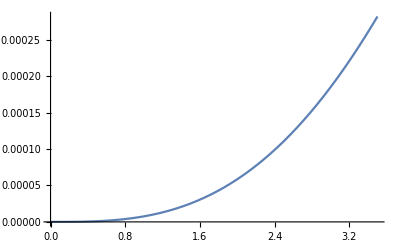

```mathematica
Plot[%61,{x,0,3.5}]
```

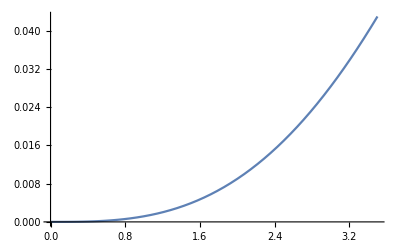

```mathematica
Plot[SphericalBesselJ[3,0.5*x],{x,0,3.5}]
```

```mathematica
6/7/17
Trail 1(correct finally! this example)
```

```mathematica
f[k_,x_]:=SphericalBesselJ[1,k*x]
```

```mathematica
f[0.35714285714285715*2*Pi,3.5]
```

0.0162114

```mathematica
NumberForm[0.01621138938277402,16]
```

0.01621138938277402

```mathematica
NumberForm[-0.15917519298168578,16]
```

-0.1591751929816858

```mathematica
NumberForm[0.27000043526828227,16]
```

0.2700004352682823

```mathematica
NumberForm[0.3289853457034173,16]
```

0.3289853457034173

```mathematica
Trail 2(bit wrong)
```

```mathematica
f[k_,x_]:=SphericalBesselJ[1,k*x]
```

```mathematica
f[0.5*2*Pi,3.5]
```

-0.00827112

```mathematica
NumberForm[-0.008271117032027545,16]
```

-0.00827111703202754

```mathematica
NumberForm[0.01621138938277402,16]
```

0.01621138938277402

```mathematica
NumberForm[-0.045031637174372266,16]
```

-0.04503163717437227

```mathematica
NumberForm[0.4052847345693511,16]
```

0.4052847345693511

```mathematica
Trail 3(l=3,k=2*pi*0.5)
```

```mathematica
f[k_,x_]:=SphericalBesselJ[3,k*x]
```

```mathematica
f[2*Pi*0.5,0.5]
```

0.0321273

```mathematica
NumberForm[0.03212733370813393,16]
```

0.03212733370813392

```mathematica
NumberForm[0.2397720978471694,16]
```

0.2397720978471694

```mathematica
NumberForm[-0.09332619911084591,16]
```

-0.0933261991108459

```mathematica
NumberForm[0.04860053153783589,16]
```

0.04860053153783589

```mathematica
7/7/2017(Nature Correct+val)

Try1. l=1,k=2*Pi*3rd
```

```mathematica
f[k_,x_]:=SphericalBesselJ[1,k*x]
```

```mathematica
-0.11038614949655379*f[0.44879896300179617,x]+-0.032030948816093946*f[1.3463968890053886,x]+
0.11466314295257264*f[2.2439948150089810,x]+
0.10704143237785343*f[3.1415927410125732,x]
```

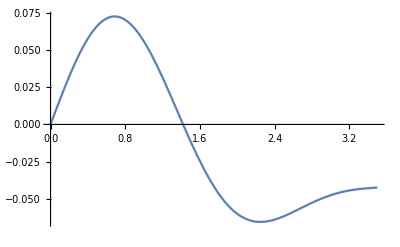

```mathematica
Plot[-0.11038614949655379 SphericalBesselJ[1,0.44879896300179617 x]-0.032030948816093946 SphericalBesselJ[1,1.3463968890053886 x]+0.11466314295257264 SphericalBesselJ[1,2.243994815008981 x]+0.10704143237785343 SphericalBesselJ[1,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
TRY 2(Nature correct)
l=1,k=4th
```

```mathematica
0.02248953*f[0.44879896300179617,x]+
0.07201814*f[1.3463968890053886,x]+
0.11845964*f[2.2439948150089810,x]+
0.16661478*f[3.1415927410125732,x]
```

0.0224895 SphericalBesselJ[1,0.448799 x]+0.0720181 SphericalBesselJ[1,1.3464 x]+0.11846 SphericalBesselJ[1,2.24399 x]+0.166615 SphericalBesselJ[1,3.14159 x]

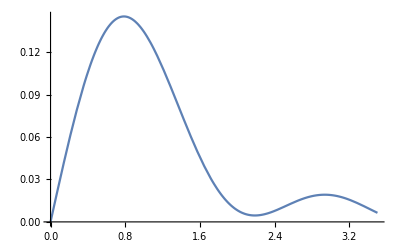

```mathematica
Plot[0.02248953 SphericalBesselJ[1,0.44879896300179617 x]+0.07201814 SphericalBesselJ[1,1.3463968890053886 x]+0.11845964 SphericalBesselJ[1,2.243994815008981 x]+0.16661478 SphericalBesselJ[1,3.1415927410125732 x],{x,0,3.5}]
```

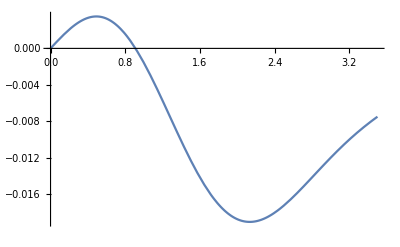

```mathematica
Plot[%4,{x,0,3.5}]
```

```mathematica
Try 3
```

```mathematica
0.17994887* SphericalBesselJ[1,0.44879896300179617 x]+0.31075267* SphericalBesselJ[1,1.3463968890053886 x]+0.14447192 *SphericalBesselJ[1,2.243994815008981 x]+0.07201814* SphericalBesselJ[1,3.1415927410125732 x]
```

0.179949 SphericalBesselJ[1,0.448799 x]+0.310753 SphericalBesselJ[1,1.3464 x]+0.144472 SphericalBesselJ[1,2.24399 x]+0.0720181 SphericalBesselJ[1,3.14159 x]

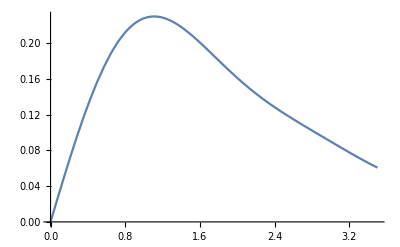

```mathematica
Plot[0.17994887 SphericalBesselJ[1,0.44879896300179617 x]+0.31075267 SphericalBesselJ[1,1.3463968890053886 x]+0.14447192 SphericalBesselJ[1,2.243994815008981 x]+0.07201814 SphericalBesselJ[1,3.1415927410125732 x],{x,0,3.5}]
```

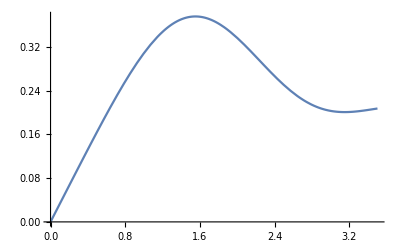

```mathematica
Plot[%7,{x,0,3.5}]
```

```mathematica
l=0,k=0th
```

```mathematica
Python
```

```mathematica
f[k_,x_]:=SphericalBesselJ[0,k*x]
```

```mathematica
3.35741331*f[0.44879896300179617,x]+
1.09395893*f[1.3463968890053886,x]+
0.75308055*f[2.2439948150089810,x]+
0.46079145*f[3.1415927410125732,x]
```

3.35741 SphericalBesselJ[0,0.448799 x]+1.09396 SphericalBesselJ[0,1.3464 x]+0.753081 SphericalBesselJ[0,2.24399 x]+0.460791 SphericalBesselJ[0,3.14159 x]

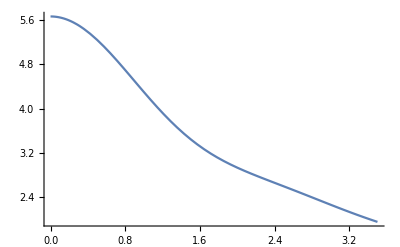

```mathematica
Plot[3.35741331 SphericalBesselJ[0,0.44879896300179617 x]+1.09395893 SphericalBesselJ[0,1.3463968890053886 x]+0.75308055 SphericalBesselJ[0,2.243994815008981 x]+0.46079145 SphericalBesselJ[0,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
MINE
```

```mathematica
15.186897989530079*f[0.44879896300179617,x]+
-8.1950863495523762*f[1.3463968890053886,x]+
-0.34491450320127159*f[2.2439948150089810,x]+
-3.6556651349810676*f[3.1415927410125732,x]
```

15.1869 SphericalBesselJ[0,0.448799 x]-8.19509 SphericalBesselJ[0,1.3464 x]-0.344915 SphericalBesselJ[0,2.24399 x]-3.65567 SphericalBesselJ[0,3.14159 x]

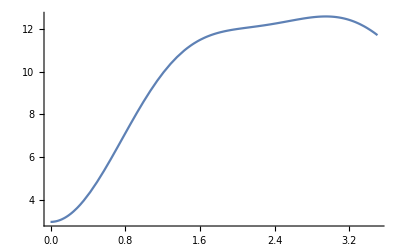

```mathematica
Plot[%20,{x,0,3.5}]
```

```mathematica
l=0,k=2nd

mine(pattern right,coeff right)
```

```mathematica
f[k_,x_]:=SphericalBesselJ[0,k*x]
```

```mathematica
-0.83508682272404600*f[0.44879896300179617,x]+
2.8726596042452890*f[1.3463968890053886,x]+
-0.072393656731186806*f[2.2439948150089810,x]+
0.74283671874646628*f[3.1415927410125732,x]
```

-0.835087 SphericalBesselJ[0,0.448799 x]+2.87266 SphericalBesselJ[0,1.3464 x]-0.0723937 SphericalBesselJ[0,2.24399 x]+0.742837 SphericalBesselJ[0,3.14159 x]

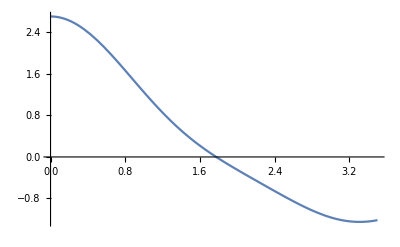

```mathematica
Plot[%24,{x,0,3.5}]
```

```mathematica
python
```

```mathematica
1.14339963*f[0.44879896300179617,x]+
1.1061926*f[1.3463968890053886,x]+
0.69454735*f[2.2439948150089810,x]+
0.50582592*f[3.1415927410125732,x]
```

1.1434 SphericalBesselJ[0,0.448799 x]+1.10619 SphericalBesselJ[0,1.3464 x]+0.694547 SphericalBesselJ[0,2.24399 x]+0.505826 SphericalBesselJ[0,3.14159 x]

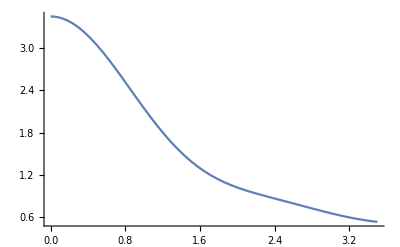

```mathematica
Plot[1.14339963 SphericalBesselJ[0,0.44879896300179617 x]+1.1061926 SphericalBesselJ[0,1.3463968890053886 x]+0.69454735 SphericalBesselJ[0,2.243994815008981 x]+0.50582592 SphericalBesselJ[0,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
l=0,k=3rd coeff

Mine
```

```mathematica
f[k_,x_]:=SphericalBesselJ[0,k*x]
```

```mathematica
0.50069381767895504*f[0.44879896300179617,x]+
-1.2550546296646754*f[1.3463968890053886,x]+
0.58862912101649845*f[2.2439948150089810,x]+
-0.51860545870521446*f[3.1415927410125732,x]
```

0.500694 SphericalBesselJ[0,0.448799 x]-1.25505 SphericalBesselJ[0,1.3464 x]+0.588629 SphericalBesselJ[0,2.24399 x]-0.518605 SphericalBesselJ[0,3.14159 x]

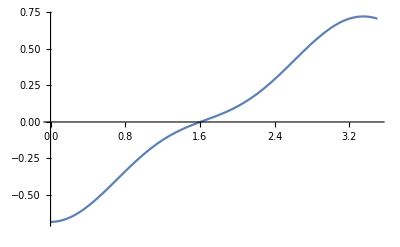

```mathematica
Plot[%31,{x,0,3.5}]
```

```mathematica
0.72686663*f[0.44879896300179617,x]+
0.69454735*f[1.3463968890053886,x]+
0.67774979*f[2.2439948150089810,x]+
0.49950692*f[3.1415927410125732,x]
```

0.726867 SphericalBesselJ[0,0.448799 x]+0.694547 SphericalBesselJ[0,1.3464 x]+0.67775 SphericalBesselJ[0,2.24399 x]+0.499507 SphericalBesselJ[0,3.14159 x]

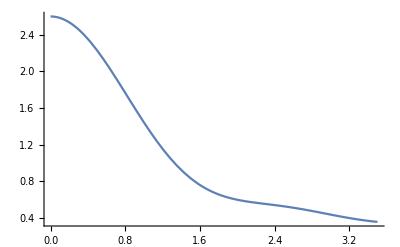

```mathematica
Plot[0.72686663 SphericalBesselJ[0,0.44879896300179617 x]+0.69454735 SphericalBesselJ[0,1.3463968890053886 x]+0.67774979 SphericalBesselJ[0,2.243994815008981 x]+0.49950692 SphericalBesselJ[0,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
l=0,k=4th
```

```mathematica
Mine
```

```mathematica
f[k_,x_]:=SphericalBesselJ[0,k*x]
```

```mathematica
-0.35753258722162323*f[0.44879896300179617,x]+
0.89497588734238354*f[1.3463968890053886,x]+
-0.24176768489817060*f[2.2439948150089810,x]+
0.76171439361350290*f[3.1415927410125732,x]
```

-0.357533 SphericalBesselJ[0,0.448799 x]+0.894976 SphericalBesselJ[0,1.3464 x]-0.241768 SphericalBesselJ[0,2.24399 x]+0.761714 SphericalBesselJ[0,3.14159 x]

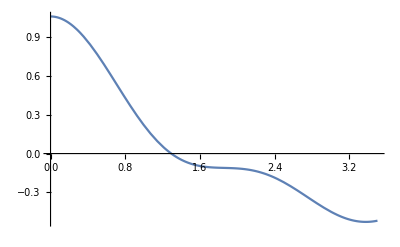

```mathematica
Plot[%38,{x,0,3.5}]
```

```mathematica
0.47909688*f[0.44879896300179617,x]+
0.50582592*f[1.3463968890053886,x]+
0.49950692*f[2.2439948150089810,x]+
0.47479888*f[3.1415927410125732,x]
```

0.479097 SphericalBesselJ[0,0.448799 x]+0.505826 SphericalBesselJ[0,1.3464 x]+0.499507 SphericalBesselJ[0,2.24399 x]+0.474799 SphericalBesselJ[0,3.14159 x]

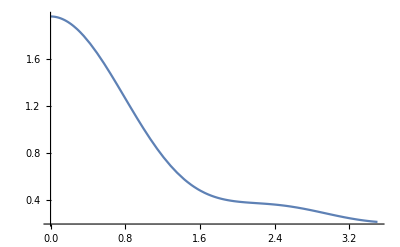

```mathematica
Plot[0.47909688 SphericalBesselJ[0,0.44879896300179617 x]+0.50582592 SphericalBesselJ[0,1.3463968890053886 x]+0.49950692 SphericalBesselJ[0,2.243994815008981 x]+0.47479888 SphericalBesselJ[0,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
L=2,k=4th
```

```mathematica
f[k_,x_]:=SphericalBesselJ[2,k*x]
```

```mathematica
-0.099978813640726291*f[0.44879896300179617,x]+
0.62866057760081639*f[1.3463968890053886,x]+
-0.50331220577217806*f[2.2439948150089810,x]+
0.53884360897238504*f[3.1415927410125732,x]
```

-0.0999788 SphericalBesselJ[2,0.448799 x]+0.628661 SphericalBesselJ[2,1.3464 x]-0.503312 SphericalBesselJ[2,2.24399 x]+0.538844 SphericalBesselJ[2,3.14159 x]

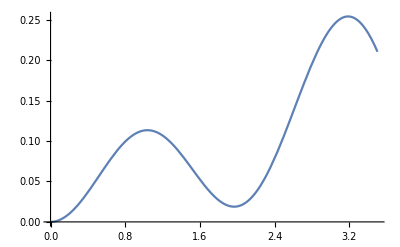

```mathematica
Plot[%48,{x,0,3.5}]
```

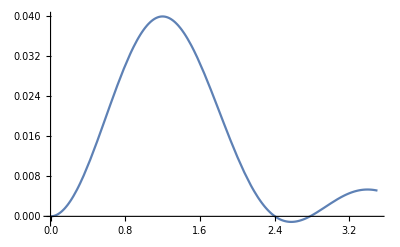

```mathematica
Plot[0.0087318 SphericalBesselJ[2,0.44879896300179617 x]+0.02005644 SphericalBesselJ[2,1.3463968890053886 x]+0.05293726 SphericalBesselJ[2,2.243994815008981 x]+0.07510847 SphericalBesselJ[2,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
L=2,k=3th
```

```mathematica
-0.058920962322231991*f[0.44879896300179617,x]+
-1.0683525861786800*f[1.3463968890053886,x]+
0.72157628594453738*f[2.2439948150089810,x]+
-0.23903992464338245*f[3.1415927410125732,x]
```

-0.058921 SphericalBesselJ[2,0.448799 x]-1.06835 SphericalBesselJ[2,1.3464 x]+0.721576 SphericalBesselJ[2,2.24399 x]-0.23904 SphericalBesselJ[2,3.14159 x]

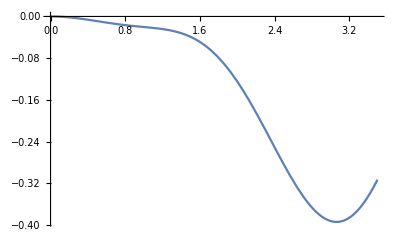

```mathematica
Plot[%54,{x,0,3.5}]
```

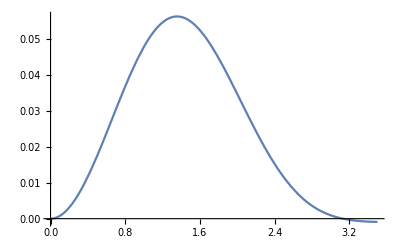

```mathematica
Plot[-0.00542356 SphericalBesselJ[2,0.44879896300179617 x]+0.04969005 SphericalBesselJ[2,1.3463968890053886 x]+0.11531949 SphericalBesselJ[2,2.243994815008981 x]+0.05293726 SphericalBesselJ[2,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
L=2,k=2th
```

```mathematica
-0.82526537424622215*f[0.44879896300179617,x]+
1.6565743551067944*f[1.3463968890053886,x]+
-0.077935704210094256*f[2.2439948150089810,x]+
0.25014506130542974*f[3.1415927410125732,x]
```

-0.825265 SphericalBesselJ[2,0.448799 x]+1.65657 SphericalBesselJ[2,1.3464 x]-0.0779357 SphericalBesselJ[2,2.24399 x]+0.250145 SphericalBesselJ[2,3.14159 x]

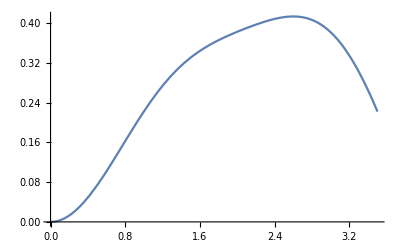

```mathematica
Plot[%60,{x,0,3.5}]
```

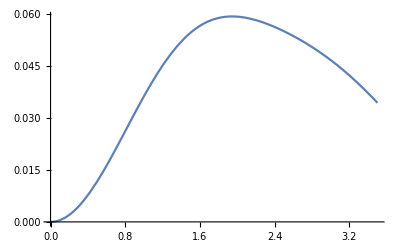

```mathematica
Plot[0.0547106 SphericalBesselJ[2,0.44879896300179617 x]+0.1690951 SphericalBesselJ[2,1.3463968890053886 x]+0.04969005 SphericalBesselJ[2,2.243994815008981 x]+0.02005644 SphericalBesselJ[2,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
L=2,k=1th
```

```mathematica
-0.32995960183522394*f[0.44879896300179617,x]+
1.1844177092711410*f[1.3463968890053886,x]+
-0.41318614821817279*f[2.2439948150089810,x]+
0.33211706941766456*f[3.1415927410125732,x]
```

-0.32996 SphericalBesselJ[2,0.448799 x]+1.18442 SphericalBesselJ[2,1.3464 x]-0.413186 SphericalBesselJ[2,2.24399 x]+0.332117 SphericalBesselJ[2,3.14159 x]

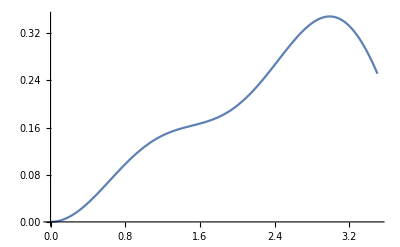

0.0256234 SphericalBesselJ[2,0.448799 x]+0.0547106 SphericalBesselJ[2,1.3464 x]-0.00542356 SphericalBesselJ[2,2.24399 x]+0.0087318 SphericalBesselJ[2,3.14159 x]

```mathematica
Plot[%67,{x,0,3.5}]
```

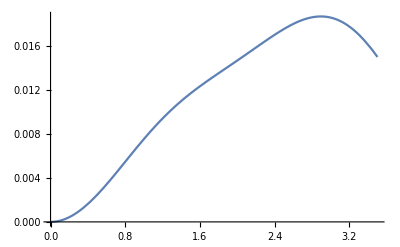

```mathematica
Plot[0.02562336 SphericalBesselJ[2,0.44879896300179617 x]+0.0547106 SphericalBesselJ[2,1.3463968890053886 x]-0.00542356 SphericalBesselJ[2,2.243994815008981 x]+0.0087318 SphericalBesselJ[2,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
L=3,k=1th
```

```mathematica
f[k_,x_]:=SphericalBesselJ[3,k*x]
```

```mathematica
-0.026543556681831088*f[0.44879896300179617,x]+
-0.079753405248992326*f[1.3463968890053886,x]+
0.11099640926813051*f[2.2439948150089810,x]+
-0.039152261456821956*f[3.1415927410125732,x]
```

-0.0265436 SphericalBesselJ[3,0.448799 x]-0.0797534 SphericalBesselJ[3,1.3464 x]+0.110996 SphericalBesselJ[3,2.24399 x]-0.0391523 SphericalBesselJ[3,3.14159 x]

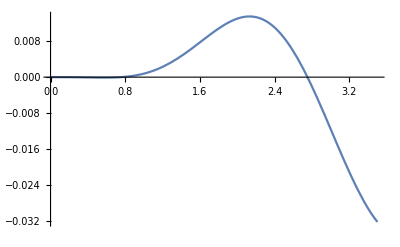

```mathematica
Plot[%75,{x,0,3.5}]
```

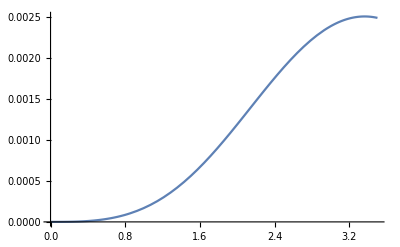

```mathematica
Plot[0.0011974 SphericalBesselJ[3,0.44879896300179617 x]+0.01020765 SphericalBesselJ[3,1.3463968890053886 x]-0.00018453 SphericalBesselJ[3,2.243994815008981 x]-0.00018453 SphericalBesselJ[3,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
L=3,k=2th
```

```mathematica
-0.23397763464287014*f[0.44879896300179617,x]+
-0.55790341234871121*f[1.3463968890053886,x]+
0.867415422204033892*f[2.2439948150089810,x]+
-0.25395296310493115*f[3.1415927410125732,x]
```

-0.233978 SphericalBesselJ[3,0.448799 x]-0.557903 SphericalBesselJ[3,1.3464 x]+0.86741542220403389 SphericalBesselJ[3,2.24399 x]-0.253953 SphericalBesselJ[3,3.14159 x]

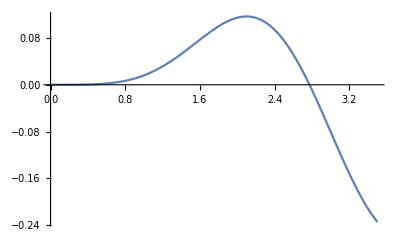

```mathematica
Plot[%81,{x,0,3.5}]
```

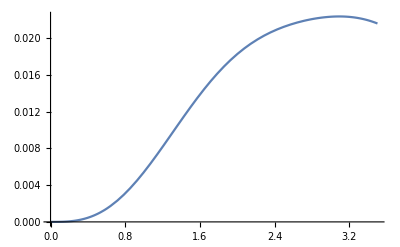

```mathematica
Plot[0.01020765 SphericalBesselJ[3,0.44879896300179617 x]+0.09584282 SphericalBesselJ[3,1.3463968890053886 x]+0.02307222 SphericalBesselJ[3,2.243994815008981 x]+0.00934024 SphericalBesselJ[3,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
L=3,k=3th
```

```mathematica
-1.6957655586791732E-002*f[0.44879896300179617,x]+
0.33912652375172286*f[1.3463968890053886,x]+
-0.21775782387127079*f[2.2439948150089810,x]+
0.22384623948260360*f[3.1415927410125732,x]
```

-4.60957-2 SphericalBesselJ[3,0.448799 x]+0.339127 SphericalBesselJ[3,1.3464 x]-0.217758 SphericalBesselJ[3,2.24399 x]+0.223846 SphericalBesselJ[3,3.14159 x]

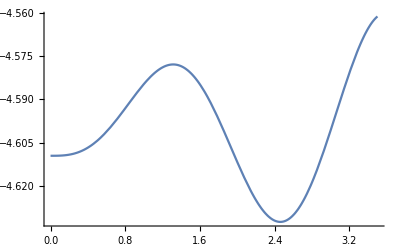

```mathematica
Plot[%88,{x,0,3.5}]
```

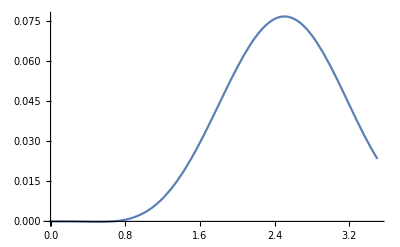

```mathematica
Plot[0.01253767 SphericalBesselJ[3,0.44879896300179617 x]+0.185662 SphericalBesselJ[3,1.3463968890053886 x]+0.18236476 SphericalBesselJ[3,2.243994815008981 x]-0.0933262 SphericalBesselJ[3,3.1415927410125732 x],{x,0,3.5}]
```

```mathematica
f[r_]:=(10^2/2-r^2/6)
```

```mathematica
Function[r,-(10^2/2-r^2/6)]
```

Function[r,-(10^2/2-r^2/6)]

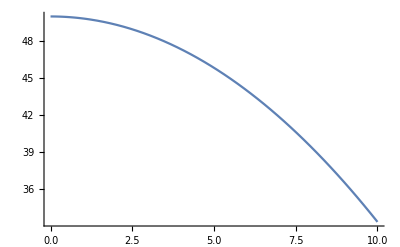

```mathematica
Plot[Function[r,(10^2/2-r^2/6)][x],{x,0,10}]
```

```mathematica
9/7/17
```

```mathematica
SphericalBesselJ[0,1.0471976*x]
```

SphericalBesselJ[0,1.0472 x]

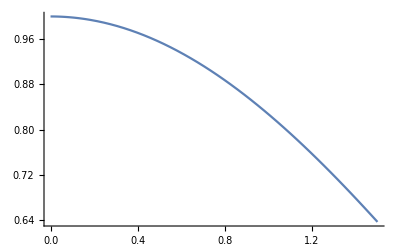

```mathematica
Plot[SphericalBesselJ[0,1.0471976 x],{x,0,1.5}]
```

```mathematica
SphericalBesselJ[0,3.1415927*x]
```

SphericalBesselJ[0,3.14159 x]

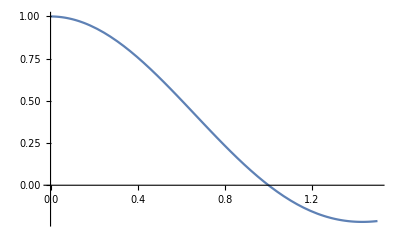

```mathematica
Plot[SphericalBesselJ[0,3.1415927 x],{x,0,1.5}]
```

```mathematica
SphericalBesselJ[2,3.1415927*x]
```

SphericalBesselJ[2,3.14159 x]

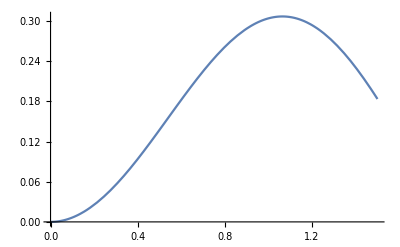

```mathematica
Plot[SphericalBesselJ[2,3.1415927 x],{x,0,1.5}]
```

```mathematica
SphericalBesselJ[2,1.0471976*x]
```

SphericalBesselJ[2,1.0472 x]

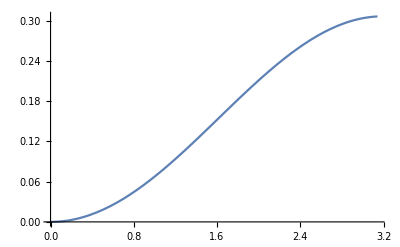

```mathematica
Plot[SphericalBesselJ[2,1.0471976 x],{x,0,Pi}]
```